## Задача 1

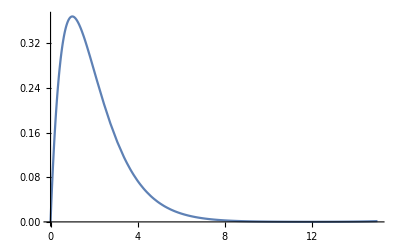

```mathematica
schrödinger=(r^2 ψ''[r])/(2*m) + q*r *ψ[r]- (l(l+1)ψ[r])/(2*m) == -ϵ r^2 ψ[r];
l = 0;
ϵ =-1;
qq=2;
m=0.5;
r0 = 15;
solution = NDSolve[{(r^2 ψ''[r])/(2*m) + qq*r *ψ[r]- (l(l+1)ψ[r])/(2*m) == -ϵ r^2 ψ[r], ψ'[10^-10]==1,ψ[10^-10] == 0}, ψ, {r, 10^-10, r0}][[1]];
Plot[ψ[r]/.solution,{r,10^-10,r0}]
```

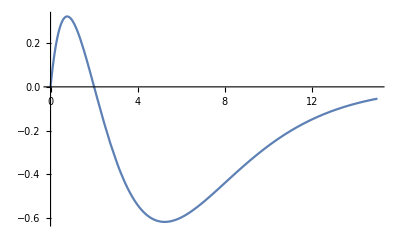

```mathematica
ϵ =-1/4;
l=0;
solution = NDSolve[{(r^2 ψ''[r])/(2*m) + qq*r *ψ[r]- (l(l+1)ψ[r])/(2*m) == -ϵ r^2 ψ[r], ψ'[10^-10]==1,ψ[10^-10] == 0}, ψ, {r, 10^-10, r0}][[1]];
Plot[ψ[r]/.solution,{r,10^-10,r0}]
```

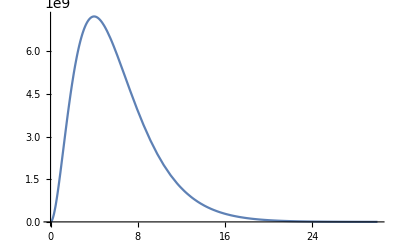

```mathematica
ϵ =-1/4;
l=1;
r0=30;
solution = NDSolve[{(r^2 ψ''[r])/(2*m) + qq*r *ψ[r]- (l(l+1)ψ[r])/(2*m) == -ϵ r^2 ψ[r], ψ'[10^-10]==1,ψ[10^-10] == 0}, ψ, {r, 10^-10, r0}][[1]];
Plot[ψ[r]/.solution,{r,10^-10,r0}]
```

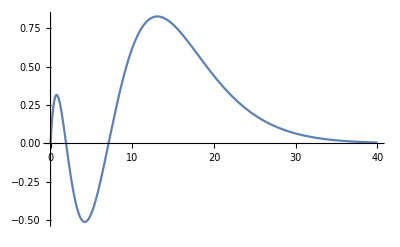

```mathematica
ϵ =-1/9;
l=0;
r0=40;
solution = NDSolve[{(r^2 ψ''[r])/(2*m) + qq*r *ψ[r]- (l(l+1)ψ[r])/(2*m) == -ϵ r^2 ψ[r], ψ'[10^-10]==1,ψ[10^-10] == 0}, ψ, {r, 10^-10, r0}][[1]];
Plot[ψ[r]/.solution,{r,10^-10,r0}]
```

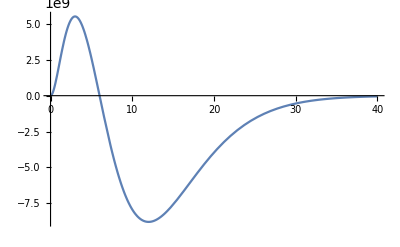

```mathematica
ϵ =-1/9;
l=1;
solution = NDSolve[{(r^2 ψ''[r])/(2*m) + qq*r *ψ[r]- (l(l+1)ψ[r])/(2*m) == -ϵ r^2 ψ[r], ψ'[10^-10]==1,ψ[10^-10] == 0}, ψ, {r, 10^-10, r0}][[1]];
Plot[ψ[r]/.solution,{r,10^-10,r0}]
```

```mathematica
ϵ =-1/9;
l=2;
r0=50;
solution = NDSolve[{(r^2 ψ''[r])/(2*m) + qq*r *ψ[r]- (l(l+1)ψ[r])/(2*m) == -ϵ r^2 ψ[r], ψ'[10^-10]==1,ψ[10^-10] == 0}, ψ, {r, 10^-10, r0}][[1]];
Plot[ψ[r]/.solution,{r,10^-10,r0}]
```

-Graphics-

## Задача 2

Строим алгебру:

```mathematica
X[x_/; x >= 2] := Expand[(-X[0])^Quotient[x, 2] X[Mod[x, 2]]];
Times[X[x_],X[y_] ] ^:= X[x+y];
Power[X[x_], n_] ^:= X[x n];
```

Проверим работу на простых примерах:

```mathematica
X[0] 
X[1]
X[2]
X[3]  
X[4]
```

X[0]

X[1]

-X[0]

-X[1]

X[0]

X[0] – это 1, X[1] – это ⅈ. Можно отобразить это в явном (красивом) виде:

```mathematica
$PrePrint= (Expand[#]/.{X[a_] :> ⅈ^a})&;
X[0]
X[1]
X[2]
X[3]  
X[4]
X[3]+X[4]
X[10]
```

1

ⅈ

-1

-ⅈ

1

1-ⅈ

-1

## Задача 4

```mathematica
HamiEq[H_,q_,p_]:= Block[ {n , i, equations},
n = Length[q];
equations = ConstantArray[0, {2, n}];
For[i = 1, i <= n, i++,
equations[[1, i]] = D[q[[i]][t], t] - D[H, p[[i]]];
equations[[2, i]] = D[p[[i]][t], t] + D[H, q[[i]]];
];
equations
];
H =(p1)^2/(2m)+(p2)^2/(2m)+V[q1^2 + q2^2]+U[q1]
TableForm[HamiEq[H, {q1,q2}, {p1,p2}] ]
```

1. p1^2+1. p2^2+U[q1]+V[q1^2+q2^2]

-2. p1+q1'[t] | -2. p2+q2'[t]
p1'[t]+U'[q1]+2 q1 V'[q1^2+q2^2] | p2'[t]+2 q2 V'[q1^2+q2^2]